## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.6; Q=0.997;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.326729+1.95956×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.555225

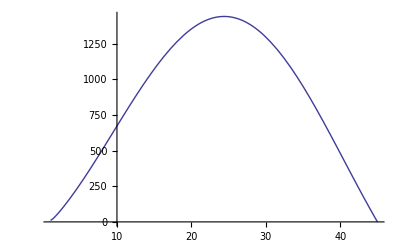

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,1.95959×10^-9},{44.8,2.01114×10^-9},{44.6,2.06674×10^-9},{44.4,2.12277×10^-9},{44.2,2.1805×10^-9},{44.,2.23998×10^-9},{43.8,2.30115×10^-9},{43.6,2.36428×10^-9},{43.4,2.42922×10^-9},{43.2,2.4995×10^-9},{43.,2.56518×10^-9},{42.8,2.63628×10^-9},{42.6,2.70955×10^-9},{42.4,2.78509×10^-9},{42.2,2.8554×10^-9},{42.,2.94324×10^-9},{41.8,3.02594×10^-9},{41.6,3.11126×10^-9},{41.4,3.19921×10^-9},{41.2,3.28993×10^-9},{41.,3.38348×10^-9},{40.8,3.47935×10^-9},{40.6,3.57947×10^-9},{40.4,3.68213×10^-9},{40.2,3.78807×10^-9},{40.,3.89717×10^-9},{39.8,4.01008×10^-9},{39.6,4.12129×10^-9},{39.4,4.24647×10^-9},{39.2,4.3704×10^-9},{39.,4.4983×10^-9},{38.8,4.63034×10^-9},{38.6,4.76664×10^-9},{38.4,4.90739×10^-9},{38.2,5.0527×10^-9},{38.,5.2029×10^-9},{37.8,5.35781×10^-9},{37.6,5.51584×10^-9},{37.4,5.68311×10^-9},{37.2,5.86091×10^-9},{37.,6.01273×10^-9},{36.8,6.21262×10^-9},{36.6,6.40082×10^-9},{36.4,6.59555×10^-9},{36.2,6.78991×10^-9},{36.,7.00465×10^-9},{35.8,7.21954×10^-9},{35.6,7.43796×10^-9},{35.4,7.67128×10^-9},{35.2,7.90883×10^-9},{35.,8.15429×10^-9},{34.8,8.40844×10^-9},{34.6,8.67076×10^-9},{34.4,8.94239×10^-9},{34.2,9.22419×10^-9},{34.,9.51397×10^-9},{33.8,9.81464×10^-9},{33.6,1.01258×10^-8},{33.4,1.04477×10^-8},{33.2,1.07721×10^-8},{33.,1.1123×10^-8},{32.8,1.14806×10^-8},{32.6,1.18517×10^-8},{32.4,1.2234×10^-8},{32.2,1.26298×10^-8},{32.,1.30397×10^-8},{31.8,1.34642×10^-8},{31.6,1.39037×10^-8},{31.4,1.43588×10^-8},{31.2,1.48302×10^-8},{31.,1.53184×10^-8},{30.8,1.58242×10^-8},{30.6,1.63482×10^-8},{30.4,1.68909×10^-8},{30.2,1.74537×10^-8},{30.,1.80365×10^-8},{29.8,1.86406×10^-8},{29.6,1.92665×10^-8},{29.4,1.99138×10^-8},{29.2,2.05879×10^-8},{29.,2.12864×10^-8},{28.8,2.20082×10^-8},{28.6,2.27568×10^-8},{28.4,2.35334×10^-8},{28.2,2.43388×10^-8},{28.,2.51726×10^-8},{27.8,2.60392×10^-8},{27.6,2.69379×10^-8},{27.4,2.78688×10^-8},{27.2,2.88357×10^-8},{27.,2.98367×10^-8},{26.8,3.08757×10^-8},{26.6,3.19647×10^-8},{26.4,3.30699×10^-8},{26.2,3.42422×10^-8},{26.,3.54339×10^-8},{25.8,3.66809×10^-8},{25.6,3.7976×10^-8},{25.4,3.93202×10^-8},{25.2,4.07132×10^-8},{25.,4.21584×10^-8},{24.8,4.36581×10^-8},{24.6,4.52128×10^-8},{24.4,4.68269×10^-8},{24.2,4.85011×10^-8},{24.,5.02371×10^-8},{23.8,5.20384×10^-8},{23.6,5.39064×10^-8},{23.4,5.58432×10^-8},{23.2,5.78533×10^-8},{23.,5.9937×10^-8},{22.8,6.20974×10^-8},{22.6,6.43378×10^-8},{22.4,6.66586×10^-8},{22.2,6.9068×10^-8},{22.,7.15633×10^-8},{21.8,7.4149×10^-8},{21.6,7.68286×10^-8},{21.4,7.96036×10^-8},{21.2,8.24783×10^-8},{21.,8.54552×10^-8},{20.8,8.85365×10^-8},{20.6,9.1726×10^-8},{20.4,9.50269×10^-8},{20.2,9.84415×10^-8},{20.,1.01968×10^-7},{19.8,1.05616×10^-7},{19.6,1.09385×10^-7},{19.4,1.13278×10^-7},{19.2,1.17296×10^-7},{19.,1.21445×10^-7},{18.8,1.25716×10^-7},{18.6,1.30121×10^-7},{18.4,1.34653×10^-7},{18.2,1.39327×10^-7},{18.,1.44128×10^-7},{17.8,1.49061×10^-7},{17.6,1.54126×10^-7},{17.4,1.59319×10^-7},{17.2,1.6464×10^-7},{17.,1.70084×10^-7},{16.8,1.75607×10^-7},{16.6,1.81325×10^-7},{16.4,1.87111×10^-7},{16.2,1.92991×10^-7},{16.,1.98964×10^-7},{15.8,2.05016×10^-7},{15.6,2.11134×10^-7},{15.4,2.17302×10^-7},{15.2,2.23507×10^-7},{15.,2.29717×10^-7},{14.8,2.35934×10^-7},{14.6,2.42094×10^-7},{14.4,2.48203×10^-7},{14.2,2.54218×10^-7},{14.,2.60103×10^-7},{13.8,2.65816×10^-7},{13.6,2.71325×10^-7},{13.4,2.7657×10^-7},{13.2,2.81504×10^-7},{13.,2.86069×10^-7},{12.8,2.90204×10^-7},{12.6,2.93839×10^-7},{12.4,2.96905×10^-7},{12.2,2.99319×10^-7},{12.,3.01×10^-7},{11.8,3.01851×10^-7},{11.6,3.01808×10^-7},{11.4,3.00642×10^-7},{11.2,2.98345×10^-7},{11.,2.94723×10^-7},{10.8,2.89557×10^-7},{10.6,2.82612×10^-7},{10.4,2.73518×10^-7},{10.2,2.61664×10^-7},{10.,2.46295×10^-7},{9.8,2.25896×10^-7},{9.6,1.98236×10^-7},{9.4,1.59363×10^-7},{9.2,1.02786×10^-7},{9.,1.71245×10^-8},{8.8,-1.17185×10^-7},{8.6,-3.33703×10^-7},{8.4,-6.9086×10^-7},{8.2,-1.29018×10^-6},{8.,-2.30784×10^-6},{7.8,-4.04926×10^-6},{7.6,-7.04217×10^-6},{7.4,-0.000012193},{7.2,-0.0000210466},{7.,-0.0000362073},{6.8,-0.000062004},{6.6,-0.000105501},{6.4,-0.000177969},{6.2,-0.00029688},{6.,-0.000488397},{5.8,-0.000790104},{5.6,-0.00125348},{5.4,-0.00194548},{5.2,-0.00294859},{5.,-0.00435942}}

```mathematica
(*The imaginary part vs the radius*)
```

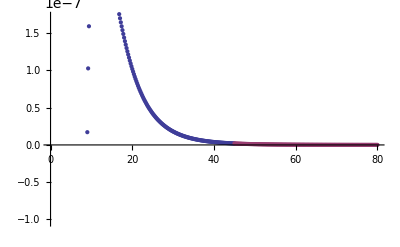

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

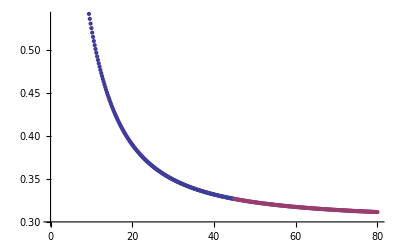

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.997/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.997/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.997/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.997/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```